# Math 223: Homework 6

Maia Powell

7 March 2021

## Problem 1

PART A: (∫_0)^x sin(π/2 t^2)dt as x → 0^+ 

We will begin by performing Integration by Parts. 
u = Sin[π/2 t^2], dv = 1dt
du = π t Cos[(π t^2)/2], v = t

(∫_0)^x sin(π/2 t^2) = Sin[π/2 t^2]t (|_0)^x- (∫_0)^x π t^2 Cos[(π t^2)/2]
= xSin[π/2 x^2]-(∫_0)^x π t^2 Cos[(π t^2)/2]

We thus find that the first term in the series is xSin[π/2 x^2].
We will now perform Integration by Parts again on the remaining integral -(∫_0)^x π t^2 Cos[(π t^2)/2].

u =  -Cos[(π t^2)/2], dv = π t^2
du = π t Sin[(π t^2)/2], v = (π t^3)/3

-(π t^3)/3Cos[(π t^2)/2] (|_0)^x- (∫_0)^x(π^2 t^4)/3Sin[(π t^2)/2]
= -(π x^3)/3Cos[(π x^2)/2]-  (∫_0)^x(π^2 t^4)/3Sin[(π t^2)/2]

We thus find that the second term in the series is -(π x^3)/3Cos[(π x^2)/2].

Thus, S(x)~ xSin[π/2 x^2]-(π x^3)/3Cos[(π x^2)/2] as x→ 0^+.

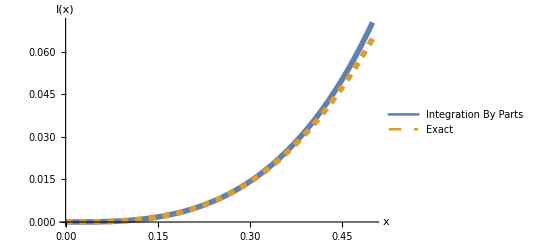

```mathematica
Plot[{(x*Sin[(π x^2)/2]-(π x^3)/3 Cos[(π x^2)/2]),FresnelS[x]},{x,0,0.5},PlotStyle->{Directive[Solid,Thickness[0.01]],Directive[Dashed,Thickness[0.01]]}, AxesLabel->{Style["x",Italic,18],Style["I(x)", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"Integration By Parts", "Exact"}]
```

PART B: (∫_0)^∞sin(π/2 t^2)dt = 1/2

Splitting the integral, we obtain: 
(∫_0)^x sin(π/2 t^2)dt + (∫_x)^∞sin(π/2 t^2)dt = 1/2
(∫_0)^x sin(π/2 t^2)dt = 1/2-(∫_x)^∞sin(π/2 t^2)dt  

Now, let u = 1/2 t^2 → du = tdt. Thus, t = √(2u) and 1/t du = dt.
Therefore, we obtain the following: 
	1/2 - (∫_X)^∞sin(π/2 t^2)dt = 1/2-(∫^∞)_(1/2 X^2) 1/(√(2u))sin(πu)du 

We now perform Integration by Parts: 
u* = 1/(√(2u)), dv* = sin(πu)
du* = -1/(2 √2 u^(3/2)), v* = -Cos[π u]/π

(∫^∞)_(1/2 X^2) 1/(√(2u))sin(πu)du = -1/(√(2u))Cos[π u]/π(|^∞)_(1/2 X^2)- (∫^∞)_(1/2 X^2)Cos[π u]/π1/(2 √2 u^(3/2))
= 1/(√(X^2))Cos[π 1/2 X^2]/π-(∫^∞)_(1/2 X^2)Cos[π u]/π1/(2 √2 u^(3/2))
=  Cos[π 1/2 X^2]/(π √(X^2))-(∫^∞)_(1/2 X^2)Cos[π u]/π1/(2 √2 u^(3/2))

Thus, S(x)~ 1/2-Cos[π 1/2 x^2]/(π √(x^2)) as x→ ∞^+.

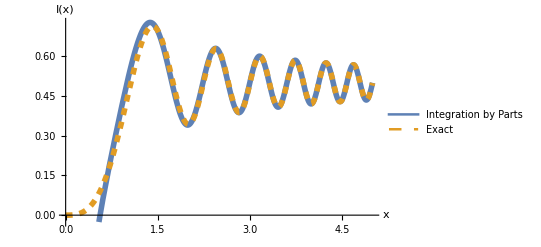

```mathematica
Plot[{1/2-Cos[π 1/2 x^2]/(π √(x^2)),FresnelS[x]},{x,0,5},PlotStyle->{Directive[Solid,Thickness[0.01]],Directive[Dashed,Thickness[0.01]]}, AxesLabel->{Style["x",Italic,18],Style["I(x)", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"Integration by Parts", "Exact"}]
```

## Problem 2

Show that (∫_0)^1(e^x-e^xt)/(1-t)dt ~ e^xlog(x)+e^x γ+..., x → +∞.

Work attached below.

```mathematica
Series[Log[x+1], x-> Infinity]
```

Log[x]+O[1/x]^1